```mathematica
Quit[]
```

## Load Rates

```mathematica
Get[NotebookDirectory[]<>"utilities.m"];
```

```mathematica
lepMass[a_Integer]:=Module[{vals={0.51099891*10^-3,105.658367*10^-3,1776.82*10^-3}},vals[[a]]];
(*Quark Masses in GeV:u,d,s,c,b,t*)

quarkMass[a_Integer]:=Module[{vals={0.003,0.006,0.1,1.3,4.3,175}},vals[[a]]];

hbar=6.58211928*10^-16*10^-9 (*GeV*s*);
clight=3*10^8;
GeVinGrams=1.782662*10^-24;

GammaApLep[mx_,ml_,ϵ_]:=Module[{αEM},αEM=1/137.035999679;
1/3*αEM*ϵ^2*mx*Sqrt[1-((2 ml)/mx)^2]*(1+(2 ml^2)/mx^2)];
Rvals=loadtxt[(NotebookDirectory[]<>"r_fixed.dat")];
RvalInt=Interpolation[Rvals,InterpolationOrder->1];
Rhad[s_]:=If[Sqrt[s]>0.36,RvalInt[Sqrt[s]],0];
(*DECAY RATES*)
GammaApHad[mx_,ϵ_]:=GammaApLep[mx,lepMass[2],ϵ]*Rhad[mx^2];
GammaAp[mx_,ϵ_]:=Re[Sum[If[lepMass[a]<mx/2,GammaApLep[mx,lepMass[a],ϵ],0.],{a,1,3}]+GammaApHad[mx,ϵ]];

tauAp[ma_,ϵ_]:=hbar*(1/GammaAp[ma,ϵ]);
ctauAp[ma_,ϵ_]:=3*10^8*hbar*100*(1/GammaAp[ma,ϵ]);
```

```mathematica
A["Pb"]=207.2;Z["Pb"]=82.;X0["Pb"]=6.37;ρ["Pb"]=11.34;
A["W"]=183.84;Z["W"]=74.;X0["W"]=6.76;ρ["W"]=19.3;
A["Al"]=26.9815386;Z["Al"]=13.;X0["Al"]=24.01;ρ["Al"]=2.7;
```

```mathematica
X0InCm[el_]:=X0[el]/ρ[el]
```

```mathematica
X0InCm["W"]
```

0.350259

```mathematica
X0InCm["Pb"]
```

0.561728

### Tests

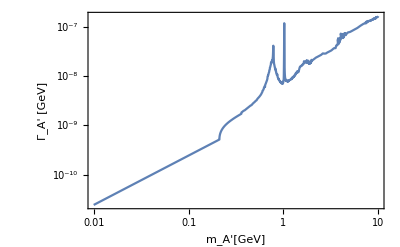

```mathematica
LogLogPlot[GammaAp[ma,10^-3],{ma,10^-2,10},FrameLabel->{"m_A'[GeV]","Γ_A' [GeV]"}]
```

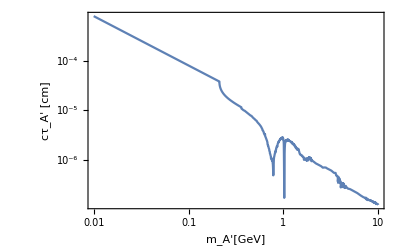

```mathematica
LogLogPlot[ctauAp[ma,10^-3],{ma,10^-2,10},FrameLabel->{"m_A'[GeV]","cτ_A' [cm]"}]
```

```mathematica
Export[NotebookDirectory[]<>"ap_ctau_eps_1.dat",{#,ctauAp[#,1]}&/@logspace[-2,1,100]]
```

/home/nblinov/Dropbox/ldmx/minimal_ap/ap_ctau_eps_1.dat

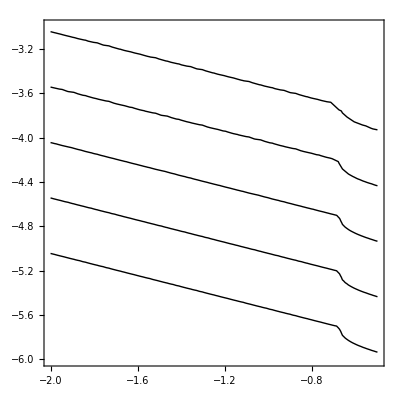

```mathematica
ContourPlot[ctauAp[10^lm,10^leps],{lm,-2,-0.5},{leps,-6,-3},Contours->{0.001,0.1,0.01,1,10},ContourShading->None,PlotRange->Full]
```

```mathematica
Simplify[ctauAp[ma,eps],Assumptions->{ma>0,ma≤0.1,ma>0.0011,0.000511<ma/2}]
```

(1.97464×10^-14)/Re[If[0.000510999<ma/2,GammaApLep[ma,lepMass[a],eps],0.]]

```mathematica
(Ea/ma)(1.974635784*^-14)/GammaApLep[ma,0,eps]
```

(8.11789×10^-12 Ea)/(eps^2 ma^2)

```mathematica
%/.{eps->10^-5,ma->0.1,Ea->8.}
```

64.9431

## Production Estimates

```mathematica
(* There are two LDMX analyses for each phase: one with production on the 10% target, and one on the 100% target *)
LDMXp1a1={Ebeam->4.,EOT->4.*10^14,T->10/100,A->184.,Z->74.,X0->6.76,dens->19.3,zmin->27.,zmax->320.};
LDMXp1a2={Ebeam->4.,EOT->4.*10^14,T->100/100,A->184.,Z->74.,X0->6.76,dens->19.3,zmin->7.,zmax->300.};
LDMXp2a1={Ebeam->8.,EOT->10^16,T->10/100,A->184.,Z->74.,X0->6.76,dens->19.3,zmin->27.,zmax->320.};
LDMXp2a2={Ebeam->8.,EOT->10^16,T->100/100,A->184.,Z->74.,X0->6.76,dens->19.3,zmin->7.,zmax->300.};
LDMX16={Ebeam->16.,EOT->10^16,T->10/100,A->184.,Z->74.,X0->6.76,dens->19.3,zmin->14.,zmax->300.};


(* Luminosity in inverse femtobarns *)
Lumi[EOT_,A_,X0_,T_]:=EOT*((6.02*10^23*X0)/A)*T*10^-39
```

```mathematica
LoadMC[fin_,experimentSpec_]:=Module[{allTab,maMin,maMax,maMinMod,MCTab,pzTab,lsigInterp,lpzInterp,sigmaMCInterp,sigmaMC,NMC,pzMC,Ebeam$,EOT$,A$,Z$,X0$,T$},
allTab=Drop[Import[fin],1];
MCTab=allTab[[;;,{1,2}]];
pzTab=allTab[[;;,{1,3}]];
maMin=Min[allTab[[;;,1]]];
maMax=Max[allTab[[;;,1]]];
(* The madgraph cross-section is buggy below about 0.02 GeV*)
maMinMod=0.001(*0.03*);
Clear[sigmaMCInterp,sigmaMC,NMC];
lsigInterp=Interpolation[Log10[MCTab],InterpolationOrder->1];
lpzInterp=Interpolation[Log10[pzTab],InterpolationOrder->1];
sigmaMCInterp[ma_]:=Which[ma≥maMinMod&&ma≤maMax,10^lsigInterp[Log10[ma]],ma<maMinMod,(maMinMod/ma)^2*10^lsigInterp[Log10[maMinMod]],ma>maMax,0.];
(*cross-section is assumed to be in pb in the input, and we convert into GeV^-2*)
sigmaMC[ma_,eps_]:=eps^2 sigmaMCInterp[ma]*10^-36/(1.97*10^-14)^2;
(*Clear[Ebeam,EOT,A,Z,X0,T];*)
{Ebeam$,EOT$,A$,Z$,X0$,T$}={Ebeam,EOT,A,Z,X0,T}/.experimentSpec;
NMC[ma_,eps_]:=Module[{me,Navo,ctau,decayFac},
Navo=6.02*10^23;
EOT$*((Navo*X0$)/A$)*T$*sigmaMC[ma,eps]*(1.97*10^-14)^2
];
pzMC[ma_]:=Which[ma≥maMinMod&&ma≤maMax,10^lpzInterp[Log10[ma]],ma>maMax,(maMax/ma)*10^lpzInterp[Log10[maMax]],ma<maMinMod,10^lpzInterp[Log10[maMinMod]]];
Return[{sigmaMC,NMC,pzMC}]
];

LoadMCWithAcceptance[finXsec_,finAcceptance_,experimentSpec_]:=Module[{acceptanceTab,logAcceptanceInterp,acceptanceInterp,allTab,MCTab,pzTab,lsigInterp,lpzInterp,sigmaMCInterp,sigmaMC,NMC,pzMC,maMin$x,maMax$x,maMin$a,maMax$a,maMinMod,ctauThrLow,ctauThrHigh,Ebeam$,EOT$,A$,Z$,X0$,T$},
(* Get acceptance in the ma vs ctau plane *)
acceptanceTab=Import[finAcceptance];
Clear[logAcceptanceInterp,acceptanceInterp];
logAcceptanceInterp=Interpolation[{{Log10[#[[1]]],Log10[#[[2]]]},Log10[Max[#[[3]],10^-200]]}&/@acceptanceTab,InterpolationOrder->1];

maMin$a=Min[acceptanceTab[[;;,1]]];
     maMax$a=Max[acceptanceTab[[;;,1]]];

ctauThrLow=Min[acceptanceTab[[;;,2]]];
ctauThrHigh=Max[acceptanceTab[[;;,2]]];

acceptanceInterp[ma_,ctau_]:=Module[{maThr,ctauLoc,m},
If[ma>maMax$a,Return[0]];
ctauLoc=Which[ctau<ctauThrLow,ctauThrLow,ctau>ctauThrHigh,ctauThrHigh,True,ctau];
m=ma(*If[ma<maMin$a,maMin$a,ma]*);
(*Print[{mAp,mApMin$a,mApMax$a}];*)
If[m>maMin$a,
Which[ctau<=ctauThrHigh&&ctau>=ctauThrLow,10^logAcceptanceInterp[Log10[m],Log10[ctau]],ctau>ctauThrHigh,(ctauThrHigh/ctau)*10^logAcceptanceInterp[Log10[m],Log10[ctauThrHigh]],ctau<ctauThrLow,0],
(* this re-scaling is valid only in the short life-time limit! Also note that ctau here is fixed and independent of ma, so there is only rescaling by one power of ma/maMin, corresponding to a rescaling of the boost factor*)
Which[ctau<=ctauThrHigh&&ctau>=ctauThrLow,(10^logAcceptanceInterp[Log10[maMin$a],Log10[ctau/(ma/maMin$a)]]),ctau>ctauThrHigh,(ctauThrHigh/ctau)*(10^logAcceptanceInterp[Log10[maMin$a],Log10[ctauThrHigh/(ma/maMin$a)]]),ctau<ctauThrLow,(10^logAcceptanceInterp[Log10[maMin$a],Log10[ctau/(ma/maMin$a)]])^((ma/maMin$a)*ctauThrLow/ctau)]]
];

(*Clear[Ebeam,EOT,A,Z,X0,T];*)
{Ebeam$,EOT$,A$,Z$,X0$,T$}={Ebeam,EOT,A,Z,X0,T}/.experimentSpec;
(*Get the cross_section*)
allTab=Import[finXsec];
MCTab=allTab[[;;,{1,2}]];
pzTab=allTab[[;;,{1,3}]];
maMin$x=Min[allTab[[;;,1]]];
maMax$x=Max[allTab[[;;,1]]];
maMinMod=0.03;

Clear[sigmaMCInterp,sigmaMC,NMC];
lsigInterp=Interpolation[Log10[MCTab],InterpolationOrder->1];
lpzInterp=Interpolation[Log10[pzTab],InterpolationOrder->1];

(*cross-section is assumed to be in pb in the input, and we convert into GeV^-2*)
sigmaMCInterp[mAp_]:=Which[mAp≥maMinMod&&mAp≤maMax$x,10^lsigInterp[Log10[mAp]],mAp<maMinMod,(maMinMod/mAp)^2*10^lsigInterp[Log10[maMinMod]],mAp>maMax$x,0.];
sigmaMC[ma_,eps_]:=eps^2 sigmaMCInterp[ma]*10^-36/(1.97*10^-14)^2;
NMC[ma_,eps_,ctau_]:=Module[{Navo,decayFac},
Navo=6.02*10^23;
EOT$*((Navo*X0$)/A$)*T$*sigmaMC[ma,eps]*acceptanceInterp[ma,ctau]*(1.97*10^-14)^2
];

pzMC[ma_]:=Which[ma≥maMinMod&&ma≤maMax$x,10^lpzInterp[Log10[ma]],ma>maMax$x,(maMax$x/ma)*10^lpzInterp[Log10[maMax$x]],ma<maMinMod,10^lpzInterp[Log10[maMinMod]]];
Return[{sigmaMC,NMC,pzMC}]
]
```

```mathematica
GenMCYieldFunc[NMC_,pzMC_,FullAccept_:False]:=Module[{YieldMC},
YieldMC[ma_,eps_,zmin_,zmax_]:=
Module[{NA,ctau,Gam,l0,decayFac,numAxions},

Gam=GammaAp[ma,eps];
ctau=3*10^8*hbar*100*(1/Gam);(*cm*)
NA=If[FullAccept,NMC[ma,eps,ctau],NMC[ma,eps]];
(*Print["Boost = ",(1-Max[me/mAp,mAp/Ebeam])*(Ebeam/2)/mRho];*)
l0=(*(1-Max[me/mAp,mAp/Ebeam])*(Ebeam/2)**)pzMC[ma]*ctau/ma;(*γcτ; Erho ~ Ebeam/2 just a hack for now*)
decayFac=If[FullAccept,1,(-ⅇ^(-zmax/l0)+ⅇ^(-zmin/l0))];
numAxions=NA*decayFac;

numAxions
];
Return[YieldMC]
];
```

```mathematica
{sigma$LDMX$8,N$LDMX$8,pz$LDMX$8}=LoadMC[(NotebookDirectory[]<>"analyze_events/xsec_and_pz_list_8gev_recoil_cut.dat"),LDMXp2a1];
{sigma$LDMX$8$FullAccept$visible,N$LDMX$8$FullAccept$visible,pz$LDMX$8$FullAccept$visible}=LoadMCWithAcceptance[(NotebookDirectory[]<>"xsec_production_8gev_no_cuts.dat"),(NotebookDirectory[]<>"analyze_events/LDMX_visible_acceptance_grid_ma_vs_ctau.dat"),LDMXp2a1];
{sigma$LDMX$8$FullAccept$visible$40rl,N$LDMX$8$FullAccept$visible$40rl,pz$LDMX$8$FullAccept$visible$40rl}=LoadMCWithAcceptance[(NotebookDirectory[]<>"xsec_production_8gev_no_cuts.dat"),(NotebookDirectory[]<>"analyze_events/LDMX_visible_acceptance_grid_ma_vs_ctau_zmin_28cm.dat"),LDMXp2a1];
{sigma$LDMX$8$FullAccept$invisible,N$LDMX$8$FullAccept$invisible,pz$LDMX$8$FullAccept$invisible}=LoadMCWithAcceptance[(NotebookDirectory[]<>"xsec_production_8gev_no_cuts.dat"),(NotebookDirectory[]<>"analyze_events/LDMX_invisible_acceptance_grid_ma_vs_ctau.dat"),LDMXp2a1];

(*====================================================================*)
(* Note that the analytical results provide a very good approximation to the MC acceptance, so no need to use the numerical ones *)
{sigma$LDMX$4$P1$Thick,N$LDMX$4$P1$Thick,pz$LDMX$4$P1$Thick}=LoadMC[(NotebookDirectory[]<>"analyze_events/xsec_and_pz_list_4gev_recoil_cut_1p2GeV.dat"),LDMXp1a2];
{sigma$LDMX$4$P1$Thin,N$LDMX$4$P1$Thin,pz$LDMX$4$P1$Thin}=LoadMC[(NotebookDirectory[]<>"analyze_events/xsec_and_pz_list_4gev_recoil_cut_1p2GeV.dat"),LDMXp1a1];
{sigma$LDMX$8$P2$Thick,N$LDMX$8$P2$Thick,pz$LDMX$8$P2$Thick}=LoadMC[(NotebookDirectory[]<>"analyze_events/xsec_and_pz_list_8gev_recoil_cut_1p2GeV.dat"),LDMXp2a2];

(* New for LDMX Theory paper, Ethr = 2.4, 4.8 GeV for 8, 16 GeV *)
{sigma$LDMX$8$P2$Thin,N$LDMX$8$P2$Thin,pz$LDMX$8$P2$Thin}=LoadMC[(NotebookDirectory[]<>"analyze_events/xsec_and_pz_list_8gev_recoil_cut_2p4GeV.dat"),LDMXp2a1];
{sigma$LDMX$16$P2$Thin,N$LDMX$16$P2$Thin,pz$LDMX$16$P2$Thin}=LoadMC[(NotebookDirectory[]<>"analyze_events/xsec_and_pz_list_16gev_recoil_cut_4p8GeV.dat"),LDMX16];

{sigma$LDMX$8$P3$Thin,N$LDMX$8$P3$Thin,pz$LDMX$8$P3$Thin}=LoadMC[(NotebookDirectory[]<>"analyze_events/xsec_and_pz_list_8gev_recoil_cut_2p4GeV.dat"),LDMX8$P3];
{sigma$LDMX$16$P3$Thin,N$LDMX$16$P3$Thin,pz$LDMX$16$P3$Thin}=LoadMC[(NotebookDirectory[]<>"analyze_events/xsec_and_pz_list_16gev_recoil_cut_4p8GeV.dat"),LDMX16$P3];

(*====================================================================*)
yield$LDMX$8=GenMCYieldFunc[N$LDMX$8,pz$LDMX$8,False];
yield$LDMX$8$FullAccept$visible=GenMCYieldFunc[N$LDMX$8$FullAccept$visible,pz$LDMX$8$FullAccept$visible,True];
yield$LDMX$8$FullAccept$visible$40rl=GenMCYieldFunc[N$LDMX$8$FullAccept$visible$40rl,pz$LDMX$8$FullAccept$visible$40rl,True];
(*==================================================================*)
yield$LDMX$4$P1$Thick = GenMCYieldFunc[N$LDMX$4$P1$Thick,pz$LDMX$4$P1$Thick,False];
yield$LDMX$4$P1$Thin = GenMCYieldFunc[N$LDMX$4$P1$Thin,pz$LDMX$4$P1$Thin,False];
yield$LDMX$8$P2$Thick = GenMCYieldFunc[N$LDMX$8$P2$Thick,pz$LDMX$8$P2$Thick,False];
yield$LDMX$8$P2$Thin = GenMCYieldFunc[N$LDMX$8$P2$Thin,pz$LDMX$8$P2$Thin,False];
```

## Projected Reach v4 (LDMX Theory Paper)

### Vanilla LDMX ( zmin = 28 cm, zmax = 300cm)

```mathematica
(* Normal colors *)
LDMXVisColor=RGBColor[0.88,0.43,0.46];
LDMXInvisColor=RGBColor[0.29,0.83,0.63];



grlvl=0.9;
```

```mathematica
(* LDMX Projections *)
visCont$P1$Thin=ContourPlot[yield$LDMX$4$P1$Thin[10^lm,10^leps,28.,300.],{lm,lmMin,-0.5},{leps,-6,2},Contours->{3},ContourShading->None,FrameLabel->{"Log(m_A/GeV)","Log_10ϵ"},ContourStyle->{{AbsoluteThickness[1.2],LDMXVisColor}},PlotRange->Full];
visCont$P2$Thin=ContourPlot[yield$LDMX$8$P2$Thin[10^lm,10^leps,28.,300.],{lm,lmMin,-0.5},{leps,-6,2},Contours->{8},ContourShading->None,FrameLabel->{"Log(m_A/GeV)","Log_10ϵ"},ContourStyle->{{AbsoluteThickness[1.2],LDMXVisColor}},PlotRange->Full];
```

InterpolatingFunction::dmval: Input value {-2.49986} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.35714} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-2.49986} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.35714} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

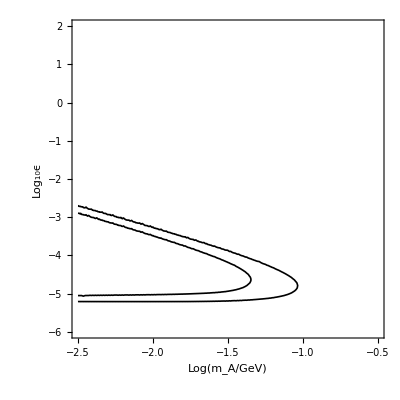

```mathematica
Show[visCont$P1$Thin,visCont$P2$Thin]
```

```mathematica
(* This is just a super naive approximation to the full calculation -- it seems in pretty good agreement *)
gammactauapprox[mA_,eps_]:=65.*(10^-5/eps)^2*(0.1/mA)^2;
NApApprox[mA_,eps_]:=6*(eps/10^-5)^2*(0.1/mA)^2;
ProbToDecay[zmin_,zmax_,γctau_]:=Exp[-zmin/γctau]-Exp[-zmax/γctau]
```

```mathematica
visCont$P2$Thin$SuperApprox=ContourPlot[NApApprox[10^lm,10^leps]*ProbToDecay[28.,300.,gammactauapprox[10^lm,10^leps]],{lm,lmMin,-0.5},{leps,-6,2},Contours->{8},ContourShading->None,FrameLabel->{"Log(m_A/GeV)","Log_10ϵ"},ContourStyle->{{AbsoluteThickness[1.2],Black,Dotted}},PlotRange->Full];
```

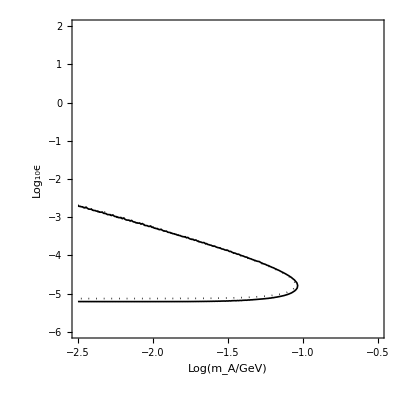

```mathematica
Show[visCont$P2$Thin$SuperApprox,visCont$P2$Thin]
```